```mathematica
Quit[]
```

```mathematica
CCxy={{Cxx,Cxy},{Cxy,Cyy}};
CC24={{C22,C24},{C24,C44}};
Ccross={{Cx2,Cx4},{Cy2,Cy4}};
```

```mathematica
meanx=Collect[Collect[Simplify[Simplify[((Ccross.Inverse[CC24].{μ2,-μ2 k3^2})[[1]])/(σ0 ν2 γ1)(1-γ3^2)/.{Cx2->σ1^2 ψ1,Cx4->-σ2^2 ψ2,C22->σ2^2,C24->-σ3^2,C44->σ4^2}]/.{μ2->ν2 σ2,k3^2->σ4/σ2 k3t^2}]/.{σ4->σ3^2/(γ3 σ2),γ1->σ1^2/(σ0 σ2)},{ψ1,ψ2},Simplify]/.{σ1^2->γ1 σ0 σ2},{ψ1,ψ2},Simplify]/.{σ2^4->γ2^2 σ1^2 σ3^2}
```

(1-k3t^2 γ3) ψ1-γ2^2 γ3 (-k3t^2+γ3) ψ2

```mathematica
Varxy=Simplify[CCxy-Ccross.Inverse[CC24].Transpose[Ccross]]/.{Cx2->σ1^2 ψ1x,Cx4->-σ2^2 ψ2x,C22->σ2^2,C24->-σ3^2,C44->σ4^2,Cxx->σ0^2,Cxy->σ0^2 ψ0r,Cyy->σ0^2,Cy2->σ1^2 ψ1y,Cy4->-σ2^2 ψ2y}//Simplify
```

{{(σ0^2 (σ3^4-σ2^2 σ4^2)+σ1^4 σ4^2 ψ1x^2-2 σ1^2 σ2^2 σ3^2 ψ1x ψ2x+σ2^6 ψ2x^2)/(σ3^4-σ2^2 σ4^2),(σ0^2 (σ3^4-σ2^2 σ4^2) ψ0r+σ1^4 σ4^2 ψ1x ψ1y+σ2^6 ψ2x ψ2y-σ1^2 σ2^2 σ3^2 (ψ1y ψ2x+ψ1x ψ2y))/(σ3^4-σ2^2 σ4^2)},{(σ0^2 (σ3^4-σ2^2 σ4^2) ψ0r+σ1^4 σ4^2 ψ1x ψ1y+σ2^6 ψ2x ψ2y-σ1^2 σ2^2 σ3^2 (ψ1y ψ2x+ψ1x ψ2y))/(σ3^4-σ2^2 σ4^2),(σ0^2 (σ3^4-σ2^2 σ4^2)+σ1^4 σ4^2 ψ1y^2-2 σ1^2 σ2^2 σ3^2 ψ1y ψ2y+σ2^6 ψ2y^2)/(σ3^4-σ2^2 σ4^2)}}

```mathematica
Collect[Simplify[Varxy[[1,1]]/σ0^2-1/.{σ3^2->γ3 σ2 σ4,σ3^4->γ3^2 σ2^2 σ4^2,ψ1x->g1ψ1x (σ0 σ2)/σ1^2,ψ2x->g1g2g3ψ2x (σ0 σ4)/σ2^2}]/.{g1ψ1x->γ1 ψ1,g1g2g3ψ2x->γ1 γ2^2 γ3 ψ2},{ψ1,ψ2}]
```

(γ1^2 ψ1^2)/(-1+γ3^2)-(2 γ1^2 γ2^2 γ3^2 ψ1 ψ2)/(-1+γ3^2)+(γ1^2 γ2^4 γ3^2 ψ2^2)/(-1+γ3^2)

```mathematica
γ1 γ2^2 γ3/.{γ1->σ1^2/(σ0 σ2),γ2^2->σ2^4/(σ1^2 σ3^2),γ3->σ3^2/(σ2 σ4)}
```

σ2^2/(σ0 σ4)

```mathematica
Collect[Simplify[(Varxy[[1,2]]/σ0^2-ψ0r)(1-γ3^2)/γ1^2/.{σ3^2->γ3 σ2 σ4,σ3^4->γ3^2 σ2^2 σ4^2,ψ1x->g1ψ1x (σ0 σ2)/σ1^2,ψ2x->g1g2g3ψ2x (σ0 σ4)/σ2^2,ψ1y->g1ψ1y (σ0 σ2)/σ1^2,ψ2y->g1g2g3ψ2y (σ0 σ4)/σ2^2}]/.{g1ψ1x->γ1 ψ1x,g1g2g3ψ2x->γ1 γ2^2 γ3 ψ2x,g1ψ1y->γ1 ψ1y,g1g2g3ψ2y->γ1 γ2^2 γ3 ψ2y},{ψ1x ψ1y,ψ1x ψ2y,ψ2x ψ2y}]
```

-ψ1x ψ1y+γ2^2 γ3^2 ψ1y ψ2x+γ2^2 γ3^2 ψ1x ψ2y-γ2^4 γ3^2 ψ2x ψ2y

## Monochromatic

```mathematica
CCxy={{Cxx,Cxy},{Cxy,Cyy}};
Ccross={{Cx2},{Cy2}};
```

```mathematica
meanx[r_]=(Ccross 1/σ2^2 μ2)[[1,1]]/.{Cx2->As ks^2 Sinc[ks r],1/σ2^2->1/(As ks^4)}
```

(μ2 Sinc[ks r])/ks^2

```mathematica
Ccross.Transpose[Ccross]
```

{{Cx2^2,Cx2 Cy2},{Cx2 Cy2,Cy2^2}}

```mathematica
Varxy[x_,y_,r_]=Simplify[CCxy-1/σ2^2 Ccross.Transpose[Ccross]/.{Cxx->As,Cyy->As,Cx2->As ks^2 Sinc[ks x],Cy2->As ks^2 Sinc[ks y],Cxy->As Sinc[ks r],1/σ2^2->1/(As ks^4)}]
```

{{As-As Sinc[ks x]^2,As (Sinc[ks r]-Sinc[ks x] Sinc[ks y])},{As (Sinc[ks r]-Sinc[ks x] Sinc[ks y]),As-As Sinc[ks y]^2}}

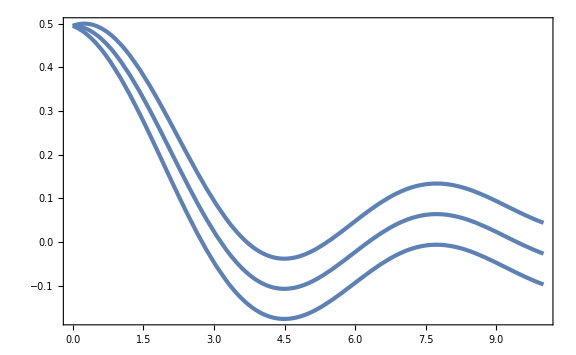

```mathematica
Plot[{meanx[r],meanx[r]+Sqrt[Varxy[r,r,0][[1,1]]],meanx[r]-Sqrt[Varxy[r,r,0][[1,1]]]}/.{μ2->7Sqrt[5 10^-3],ks->1,As->5 10^-3},{r,0,10}]
```

```mathematica
tpf[x_,y_,r_]=Varxy[x,y,r][[1,2]]+meanx[x]meanx[y]
```

(μ2^2 Sinc[ks x] Sinc[ks y])/ks^4+As (Sinc[ks r]-Sinc[ks x] Sinc[ks y])

```mathematica
-1/r Integrate[meanx[ρ] ρ^2,{ρ,0,r}]
```

-(μ2 (-ks r Cos[ks r]+Sin[ks r]))/(ks^5 r)

```mathematica
rxy[x_,y_,θx_,θy_,ϕx_,ϕy_]=Sqrt[(x{Sin[θx]Cos[ϕx],Sin[θx]Sin[ϕx],Cos[θx]}-y{Sin[θy]Cos[ϕy],Sin[θy]Sin[ϕy],Cos[θy]}).(x{Sin[θx]Cos[ϕx],Sin[θx]Sin[ϕx],Cos[θx]}-y{Sin[θy]Cos[ϕy],Sin[θy]Sin[ϕy],Cos[θy]})//FullSimplify]
```

√(x^2+y^2-2 x y (Cos[θx] Cos[θy]+Cos[ϕx-ϕy] Sin[θx] Sin[θy]))

```mathematica
tpf[x,y,rxy[x,y,θx,θy,ϕx,dϕ+ϕx]]
```

(μ2^2 Sinc[ks x] Sinc[ks y])/ks^4+As (-Sinc[ks x] Sinc[ks y]+Sinc[ks √(x^2+y^2-2 x y (Cos[θx] Cos[θy]+Cos[dϕ] Sin[θx] Sin[θy]))])

```mathematica
Integrate[tpf[x,y,rxy[x,y,θx,θy,ϕx,dϕ+ϕx]] x^2 y^2 Sin[θx]Sin[θy](*,{x,0,r},{θx,0,π}*),{dϕ,0,2π}(*,{y,0,r},{θy,0,π},{ϕy,0,2π}*)]
```

$Aborted